# Ideal Two-Component Systems

## Pressure Composition Diagrams (P-x-y)

## Raoult’s Law

For a more detailed explanation of Raoult’s law, please view Raoult’s Law Explanation.

Raoult’s law is used to calculate the bubble point (BP) and dew point (DP) cures of a mixture in vapor liquid equilibrium. The equations for these curves are shown below:

P_BP=x_1 P_1^sat+(1-x_1) P_2^sat

P_DP=1/(y_1/P_1^sat+(1-y_1)/P_2^sat)

#### Derivation of Raoult’s Law

Raoult’s law states that for a binary mixture:

P=x_1 P_1^sat+x_2 P_2^sat		(1)

Equation (1) can be rewritten to eliminate the x_2 term.

P=x_1 P_1^sat+(1-x_1) P_2^sat	(2)

The Antoine equation is used to get the saturation pressures of each component (P_1^sat and P_2^sat).

log_10(P_i^sat)=A-B/(T+C)		(3)

In equation (3) A, B, and C are constants specific to each component. Thir values can be found in tabulated data.

For the bubble point (BP) calculation ∑K_i x_i=1 is used to find the BP pressure. K_i is caled the K-ratio of component i; according to Raoult’s law, K_i is the ratio of the component partial pressure to the total pressure K_i=P_i^sat/P.

1=P_1^sat/P x_1+P_2^sat/P (1-x_1)	(4)

Multiplying equation (4) through by P will return equation (1).

For the dew point (DP) calculation, ∑y_i/K_i=1 is used to calculate the DP pressure.

y_1 P/P_1^sat+(1-y_1) P/P_2^sat=1	(5)

Rearraanging equation (5) to solve for pressure as a function of the molar composition in the vapor phase (of the more volatile component, 1) is the DP pressure.

P=1/(y_1/P_1^sat+(1-y_1)/P_2^sat)			(6)

## Mapping a P-x-y Diagram

The blue line represents the bubble-point, above this line at higher pressures both components are in the liquid phase. Likewise, the green line represents the dew-point, below this line both components are in the vapor phase. Inside the shaded region between the two curves is the 2-phase region. The amount of each phase that is present at a certain composition in the 2-phase region is determined from the lever rule.

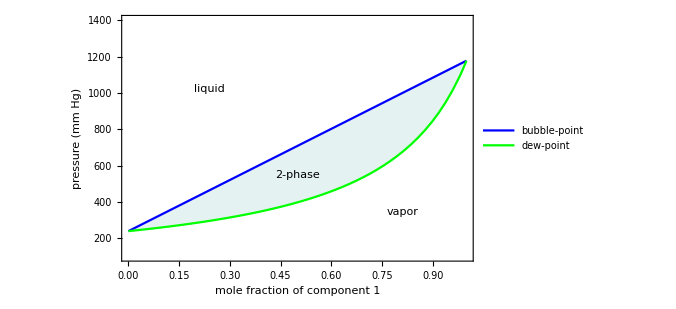

```mathematica
Framed[Module[{Psat1,Psat2,Px,Py},
Psat1=10^(6.90565-1211.033/(95+220.79)); 
Psat2=10^(6.65464-1344.8/(95+219.48)); 
Px[x_]=x*Psat1+(1-x)*Psat2;
Py[x_]=(x/Psat1+(1-x)/Psat2)^-1;
Plot[{Px[x],Py[x]},{x,0,1},PlotStyle->{{Thick,Blue},{Thick,Green}},PlotRange->{{0,1},{100,1400}},Frame->True,FrameLabel->{Style["mole fraction of component 1",16],Style["pressure (mm Hg)",16]},LabelStyle->Black,AxesOrigin->{0,100},ImageSize->500,PlotLegends->Placed[LineLegend[{Style["bubble-point",15],Style["dew-point",15]}],Above],Filling->{1->{{2},Opacity[0.1,Blend[{Blue,Green},0.5]]}},
Epilog->{
Inset[Text@Style["liquid",18,Darker[Gray,0.4]],Scaled[{0.25,0.7}]],
Inset[Text@Style["vapor",18,Darker[Gray,0.4]],Scaled[{0.8,0.2}]],
Inset[Text@Style["2-phase",18,Darker[Gray,0.4]],Scaled[{0.5,0.35}]]
}]]]
```

## Lever Rule

The lever rule is used to determine the relative amounts of liquid and vapor in the system. An explanation of the lever rule is shown in this Screencast.
 
Mouseover the plot below to see the points used in the lever rule calculations.

	f^L=(y_1-z_1)/(y_1-x_1)	liquid amount present at z_1
	f^V=(x_1-z_1)/(x_1-y_1)	vapor amount present at z_1

```mathematica
Framed@Module[{T,p,Psat1,Psat2,Px,Py,x1,y1,leverx,levery,p1,p2,p3},
T=95;
p=550;
Psat1=10^(6.90565-1211.033/(T+220.79)); 
Psat2=10^(6.65464-1344.8/(T+219.48)); 
Px[x_]=x*Psat1+(1-x)*Psat2;
Py[x_]=(x/Psat1+(1-x)/Psat2)^-1;
x1=X/.FindRoot[p==X*Psat1+(1-X)*Psat2,{X,0}];
y1=Y/.FindRoot[p==1/(Y/Psat1+(1-Y)/Psat2),{Y,0}];
leverx=Which[
x1<0.4<y1,(y1-0.4)/(y1-x1),
Px[0.4]≤p,1,
Py[0.4]≥p,0];
levery=1-leverx;
p1=Plot[{Px[x],Py[x]},{x,0,1},PlotStyle->{{Thick,Blue},{Thick,Green}},PlotRange->{{0,1},{100,1400}},Frame->True,FrameLabel->{Style["mole fraction of component 1",16],Style["pressure (mm Hg)",16]},LabelStyle->Black,AxesOrigin->{0,100},ImageSize->500,
Epilog->Inset[Graphics[{PointSize[0.05],Point[{0,0}]}],{0.4,p}]];
p2=Graphics[{
{Thick,Dashed,Blue,Line[{{x1,p},{0.4,p}}]},
{Thick,Dashed,Green,Line[{{0.4,p},{y1,p}}]},
{Thickness[0.005],Line[{{x1,p},{x1,p+40},{0.39,p+40},{0.39,p}}]},{Thickness[0.005],Line[{{(x1+0.4)/2,p+40},{(x1+0.4)/2,p+400}}]},
{Thickness[0.005],Line[{{0.41,p},{0.41,p+40},{y1,p+40},{y1,p}}]},{Thickness[0.005],Line[{{(0.4+y1)/2,p+40},{(0.4+y1)/2,p+400}}]},
Text[Style[Column[{Row[{NumberForm[leverx*100,2],"%"}],"liquid"},Alignment->Center],16],{(y1+0.4)/2,p+500}],
Text[Style[Column[{Row[{NumberForm[levery*100,2],"%"}],"vapor"},Alignment->Center],16],{(x1+0.4)/2,p+500}]
}];
p3=Graphics[{
{Thick,Dashed,Blue,Line[{{x1,p},{0.4,p}}]},
{Thick,Dashed,Green,Line[{{0.4,p},{y1,p}}]},
{Thickness[0.005],Line[{{x1,p},{x1,p+40},{0.39,p+40},{0.39,p}}]},{Thickness[0.005],Line[{{(x1+0.4)/2,p+40},{(x1+0.4)/2,p+400}}]},
{Thickness[0.005],Line[{{0.41,p},{0.41,p+40},{y1,p+40},{y1,p}}]},{Thickness[0.005],Line[{{(0.4+y1)/2,p+40},{(0.4+y1)/2,p+400}}]},
Text[Style["L",16],{(y1+0.4)/2,p+450}],
Text[Style["V",16],{(x1+0.4)/2,p+450}],
{PointSize[0.015],Point[{x1,p}]},Text[Style["x_1",17],{x1,p},{-1,1}],
{PointSize[0.015],Point[{0.4,p}]},Text[Style["z_1",17],{0.415,p},{-1,1}],
{PointSize[0.015],Point[{y1,p}]},Text[Style["y_1",17],{y1,p},{-1,1}]
}];
Mouseover[Show[p1,p2],Show[p1,p3]]]
```

### Concept Test #1

Based on the ideal mixture in the above P-x-y diagram, use the lever rule to calculate the amount of liquid and vapor present for an overal molar composition z_1=0.6. Note that the composition of component 1 in the liquid phase at constant pressure is x_1=0.33 and in the vapor phase, y_1=0.71.

#### Solution

The fraction of liquid present (f^L) is,

	f^L=L/(L+V)=(z_1-y_1)/(x_1-y_1)=(0.6-0.71)/(0.33-0.71)=0.29   or  29%   liquid
	
The fraction of vapor present (f^V) is,

	f^V=V/(L+V)=(z_1-x_1)/(y_1-x_1)=(0.6-0.33)/(0.71-0.33)=0.71   or  71%  vapor
	
Use the Demonstration below to see how the amount of liquid and vapos present changes with overall compositon.

```mathematica
Manipulate[
Module[{T,p,Psat1,Psat2,Px,Py,x1,y1,leverx,levery,p1,p2,p3},
T=95;
p=550;
Psat1=10^(6.90565-1211.033/(T+220.79)); 
Psat2=10^(6.65464-1344.8/(T+219.48)); 
Px[x_]=x*Psat1+(1-x)*Psat2;
Py[x_]=(x/Psat1+(1-x)/Psat2)^-1;
x1=X/.FindRoot[p==X*Psat1+(1-X)*Psat2,{X,0}];
y1=Y/.FindRoot[p==1/(Y/Psat1+(1-Y)/Psat2),{Y,0}];
leverx=Which[
x1<comp<y1,(y1-comp)/(y1-x1),
Px[comp]≤p,1,
Py[comp]≥p,0];
levery=1-leverx;
p1=Plot[{Px[x],Py[x]},{x,0,1},PlotStyle->{{Thick,Blue},{Thick,Green}},PlotRange->{{0,1},{100,1400}},Frame->True,FrameLabel->{Style["mole fraction of component 1",16],Style["pressure (mm Hg)",16]},LabelStyle->Black,AxesOrigin->{0,100},ImageSize->500,
Epilog->Inset[Graphics[{PointSize[0.05],Point[{0,0}]}],{comp,p}]];
p2=Graphics[{
{Thick,Dashed,Blue,Line[{{x1,p},{comp,p}}]},
{Thick,Dashed,Green,Line[{{comp,p},{y1,p}}]},
If[comp>0.33,{Thickness[0.0045],Line[{{x1,p},{x1,p+40},{comp-0.01,p+40},{comp-0.01,p}}]}],{Thickness[0.0045],Line[{{(x1+comp)/2,p+40},{(x1+comp)/2,p+400}}]},
If[comp<0.71,{Thickness[0.0045],Line[{{comp+0.01,p},{comp+0.01,p+40},{y1,p+40},{y1,p}}]}],{Thickness[0.0045],Line[{{(comp+y1)/2,p+40},{(comp+y1)/2,p+400}}]},
Text[Style[Column[{Row[{NumberForm[leverx*100,2],"%"}],"liquid"},Alignment->Center],16],{(y1+comp)/2,p+500}],
Text[Style[Column[{Row[{NumberForm[levery*100,2],"%"}],"vapor"},Alignment->Center],16],{(x1+comp)/2,p+500}]
}];
p3=Graphics[{
{Thickness[0.003425],Line[{{0.05+(y1+comp)/2,400},{(y1+comp)/2,p}}]},
Text[Framed[Style["f^L=L/(L + V)",16],Background->White],{(y1+comp)/2,300},{-1,0}],
{Thickness[0.003425],Line[{{-0.05+(x1+comp)/2,400},{(x1+comp)/2,p}}]},
Text[Framed[Style["f^V=V/(L + V)",16],Background->White],{(x1+comp)/2,300},{1,0}]
}];
Show[p1,p2,p3]],
{{comp,0.6,"overall molar composition (z_1)"},0.33,0.71,0.01,Appearance->"Labeled"}]
```

## Changes in Pressure

For an ideal mixture at a constant overall composition (z_1=0.5), see how varying the pressure affects the amount of liquid and vapor present, and the composiaions in each phase.

### Effect on Liquid and Vapor Amounts

As pressure increases at constant composition, the binary mixture is compressed and thus goes from the vapor phase to liquid phase.

```mathematica
Manipulate[
Module[{T,Psat1,Psat2,Px,Py,x1,y1,leverx,levery,p1,p2,p3},
T=95;
Psat1=10^(6.90565-1211.033/(T+220.79)); 
Psat2=10^(6.65464-1344.8/(T+219.48)); 
Px[x_]=x*Psat1+(1-x)*Psat2;
Py[x_]=(x/Psat1+(1-x)/Psat2)^-1;
x1=X/.FindRoot[p==X*Psat1+(1-X)*Psat2,{X,0}];
y1=Y/.FindRoot[p==1/(Y/Psat1+(1-Y)/Psat2),{Y,0}];
leverx=Which[
x1<0.5<y1,(y1-0.5)/(y1-x1),
Px[0.5]≤p,1,
Py[0.5]≥p,0];
levery=1-leverx;
p1=Plot[{Px[x],Py[x]},{x,0,1},PlotStyle->{{Thick,Blue},{Thick,Green}},PlotRange->{{0,1},{100,1400}},Frame->True,FrameLabel->{Style["mole fraction of component 1",16],Style["pressure (mm Hg)",16]},LabelStyle->Black,AxesOrigin->{0,100},ImageSize->450,
Epilog->Inset[Graphics[{PointSize[0.09],Point[{0,0}]}],{0.5,p}]];
p2=BarChart[{leverx,levery},ChartStyle->{Blue,Green},ChartLayout->"Stacked",AspectRatio->Full,ImageSize->{100,290},ChartLabels->Placed[{Framed[Style[Row[{NumberForm[100*leverx,{3,0}]," % L"}],15,Bold],Background->White],Framed[Style[Row[{NumberForm[100*levery,{3,0}]," % V"}],15,Bold],Background->White]},Center]];
p3=Graphics[{
If[leverx==1∨levery==1,Text[""],
{{Thick,Dashed,Blue,Line[{{x1,p},{0.5,p}}]},
{Thick,Dashed,Green,Line[{{0.5,p},{y1,p}}]}}]
}];
Row[{Show[p1,p3],Show[p2]}]
],
{{p,530,"pressure (mm Hg)"},200,1000,5,Appearance->"Labeled"}]
```

### Effect on Molar Composition in the Liquid and Vapor Phases

#### Concept Test #2

A piston-cylinder system contains components A and B in vapor-liquid equilibrium (VLE). Assume the solution and gas are ideal, with x_A=0.25 and y_A=0.5. A small weight is added to the piston, while temperature is help constant. What happens to the system as pressure increases?

A. x_A increases, y_A decreases
B. x_A increases, y_A increases
C. x_A decreases, y_A decreases
D. x_A decreases, y_A increases

```mathematica
Framed@Graphics3D[{
{Opacity[0.3],Cylinder[{{0,0,0},{0,0,2}},0.75]},
{Gray,Cylinder[{{0,0,1.5},{0,0,1.75}},0.75]},
{Lighter[Blue,0.6],Cylinder[{{0,0,0},{0,0,0.55}},0.75]},
{FaceForm[Black],Cuboid[{-0.25,0,2.25},{0.25,0,2.65}]},
{Thickness[0.02],Arrowheads[0.05],Arrow[{{0,0,2.25},{0,0,1.85}}]},
Text[Style[Column[{"vapor","y_A = 0.5"},Alignment->Center],18],{0,0,1.}],
Text[Style[Column[{"liquid","x_A = 0.25"},Alignment->Center],18],{0,0,0.15}]
},Boxed->False,ViewPoint->Front,Lighting->{{"Ambient",LightGray}},ImageSize->150]
```

-Graphics3D-

##### Solution

B. x_A and y_A increase. For a complete solution, view this Screencast.

```mathematica
Manipulate[
Module[{T,Psat1,Psat2,Px,Py,x1,y1,leverx,levery,p1,p2,p3},
T=95;
Psat1=10^(6.90565-1211.033/(T+220.79)); 
Psat2=10^(6.65464-1344.8/(T+219.48)); 
Px[x_]=x*Psat1+(1-x)*Psat2;
Py[x_]=(x/Psat1+(1-x)/Psat2)^-1;
x1=X/.FindRoot[p==X*Psat1+(1-X)*Psat2,{X,0}];
y1=Y/.FindRoot[p==1/(Y/Psat1+(1-Y)/Psat2),{Y,0}];
leverx=Which[
x1<0.5<y1,(y1-0.5)/(y1-x1),
Px[0.5]≤p,1,
Py[0.5]≥p,0];
levery=1-leverx;
p1=Plot[{Px[x],Py[x]},{x,0,1},PlotStyle->{{Thick,Blue},{Thick,Green}},PlotRange->{{0,1},{100,1400}},Frame->True,FrameLabel->{Style["mole fraction of component 1",16],Style["pressure (mm Hg)",16]},LabelStyle->Black,AxesOrigin->{0,100},ImageSize->500,
Epilog->Inset[Graphics[{PointSize[0.055],Point[{0,0}]}],{0.5,p}]];
p3=Graphics[{
{Thick,Dashed,Blend[{Blue,Gray},0.65],Line[{{0.310296,530},{0.5,530}}]},
{Thick,Dashed,Blend[{Green,Gray},0.65],Line[{{0.5,530},{0.688999,530}}]},
{Thick,Dashed,Blend[{Blue,Gray},0.65],Line[{{0.310296,530},{0.310296,100}}]},
{Thick,Dashed,Blend[{Green,Gray},0.65],Line[{{0.688999,530},{0.688999,100}}]},

{Gray,PointSize[0.02],Point[{0.5,530}]},

{Thick,Dashed,Blue,Line[{{x1,p},{0.5,p}}]},
{Thick,Dashed,Green,Line[{{0.5,p},{y1,p}}]},
{Thick,Dashed,Blue,Line[{{x1,p},{x1,100}}]},
{Thick,Dashed,Green,Line[{{y1,p},{y1,100}}]},
If[p==530,Text@"",
{{Thick,Arrow[{{0.310296,150},{x1,150}}]},
{Thick,Arrow[{{0.688999,150},{y1,150}}]}}]
}];
Show[p1,p3]
],
{{p,530,"pressure (mm Hg)"},400,705,5,Appearance->"Labeled"}]
```